## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initialize Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TALA2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data_MD.csv";

mainFolder = "TALA2_param_inf2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/TALA2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(g3p^c+s7p^c⇌e4p^c+f6p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
s7p | Null | 1.31 | 1.2445
1.3755 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | r5p | 0.031 | 0.02945
0.03255 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 71.4 | 67.83
74.97 | 1/s | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 79.4 | 75.43
83.37 | 1/s | 8.5 | 30 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | e4p | 0.00009
Competitive | g3p | 0.000038
Competitive | f6p | 0.0012
Competitive | s7p | 0.000285 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,0, 1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities={1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+s7p^c⇌e4p^c+f6p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
s7p | Null | 1.31 | 1.2445
1.3755 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 71.4 | 67.83
74.97 | 1/s | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 79.4 | 75.43
83.37 | 1/s | 8.5 | 30 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | e4p | 0.00009
Competitive | g3p | 0.000038
Competitive | f6p | 0.0012
Competitive | s7p | 0.000285 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
{{"Ping Pong Bi Bi"}, {"\"[f6p,g3p,e4p,s7p]\""}}
```

```mathematica
(*catalyticBranch={"E_TALA2[c] + f6p[c] <=> E_TALA2[c]&f6p",
				"E_TALA2[c]&f6p <=> E_TALA2[c]&mod&g3p",
				"E_TALA2[c]&mod&g3p <=> E_TALA2[c]&mod + g3p[c]",
                "E_TALA2[c]&mod + e4p[c] <=> E_TALA2[c]&mod&e4p",
				"E_TALA2[c]&mod&e4p <=> E_TALA2[c]&s7p",
				"E_TALA2[c]&s7p <=> E_TALA2[c] + s7p[c]"};*)

catalyticBranch={"E_TALA2[c] + s7p[c] <=> E_TALA2[c]&s7p",
				"E_TALA2[c]&s7p <=> E_TALA2[c]&mod&e4p",
				"E_TALA2[c]&mod&e4p <=> E_TALA2[c]&mod + e4p[c]",
                                      "E_TALA2[c]&mod + g3p[c] <=> E_TALA2[c]&mod&g3p",
				"E_TALA2[c]&mod&g3p <=> E_TALA2[c]&f6p",
				"E_TALA2[c]&f6p <=> E_TALA2[c] + f6p[c]"};



enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((TALA2^c)_^+s7p^c⇌(TALA2^c&s7p^c)_^)^TALA21,((TALA2^c&s7p^c)_^⇌(TALA2^c&mod^c&e4p^c)_^)^TALA22,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&mod^c)_^+e4p^c)^TALA23,((TALA2^c&mod^c)_^+g3p^c⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&f6p^c)_^)^TALA25,((TALA2^c&f6p^c)_^⇌(TALA2^c)_^+f6p^c)^TALA26}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"]
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

{((TALA2^c)_^+s7p^c⇌(TALA2^c&s7p^c)_^)^TALA21,((TALA2^c&s7p^c)_^⇌(TALA2^c&mod^c&e4p^c)_^)^TALA22,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&mod^c)_^+e4p^c)^TALA23,((TALA2^c&mod^c)_^+g3p^c⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&f6p^c)_^)^TALA25,((TALA2^c&f6p^c)_^⇌(TALA2^c)_^+f6p^c)^TALA26}

```mathematica
mechanism
```

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc=1;
simplifyFlag=True;
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};
mechanism="PingPong";

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites,assumedSaturatingConc,mechanism];
```

{TALA22,TALA25}

in

{TALA22}

Added inhibition reactions:

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

Generating flux equation...

{((TALA2^c&s7p^c)_^-((TALA2^c&mod^c&e4p^c)_^)/K_TALA22) Volume_c k_TALA22^⟶}

Volume_c (-(TALA2^c&mod^c&e4p^c)_^ k_TALA22^⟵+(TALA2^c&s7p^c)_^ k_TALA22^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
customRatiosDataList={{1,( Subscript[k, TALA21]^⟶/Subscript[k, TALA21]^⟵)*(Subscript[k, TALA22]^⟶/Subscript[k, TALA22]^⟵),1299934,{51044, 33105138}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	3.7999999999999996e-6	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.09090909090909091
1	0	0	6.022594131352233e-6	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.13680688860321005
1	0	0	9.545168439736411e-6	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.20076000891310186
1	0	0	0.000015128072481032882	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.2847472489508012
1	0	0	0.00002397637909024733	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0	0.000037999999999999995	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0	0.000060225941313522335	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.6131368201531431
1	0	0	0.00009545168439736412	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0	0.00015128072481032897	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0	0.0002397637909024733	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0	0.00037999999999999997	1	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.9090909090909091
1	9.000000000000007e-6	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.09090909090909098
1	0.000014264038732150038	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.13680688860321014
1	0.000022606977883586257	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.20076000891310197
1	0.00003582964534981475	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.2847472489508014
1	0.00005678616100321741	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.38686317984685703
1	0.00009000000000000007	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.5000000000000002
1	0.00014264038732150037	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.6131368201531432
1	0.00022606977883586258	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.7152527510491988
1	0.00035829645349814786	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.7992399910868985
1	0.0005678616100321741	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.86319311139679
1	0.0009000000000000007	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.9090909090909093
1	1	0.00011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.09090909090909088
1	1	0.00019018718309533363	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.13680688860321
1	1	0.0003014263717811494	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.20076000891310164
1	1	0.0004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.28474724895080133
1	1	0.0007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.38686317984685703
1	1	0.0011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.49999999999999994
1	1	0.0019018718309533362	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.613136820153143
1	1	0.0030142637178114944	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.7152527510491984
1	1	0.004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.7992399910868982
1	1	0.007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.8631931113967899
1	1	0.011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.9090909090909092
1	0	0	1	0.0000285	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.09090909090909093
1	0	0	1	0.000045169455985141756	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.13680688860321005
1	0	0	1	0.00007158876329802309	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.2007600089131019
1	0	0	1	0.00011346054360774674	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.28474724895080145
1	0	0	1	0.000179822843176855	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.38686317984685686
1	0	0	1	0.000285	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.5
1	0	0	1	0.00045169455985141755	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.6131368201531432
1	0	0	1	0.000715887632980231	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.7152527510491988
1	0	0	1	0.0011346054360774674	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.7992399910868982
1	0	0	1	0.00179822843176855	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.86319311139679
1	0	0	1	0.00285	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.9090909090909091
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	9.000000000000007e-6	1	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.06250000000000004
1	0.000028460498941515435	1	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.17411239489546843
1	0.00009000000000000007	1	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.40000000000000013
1	0.00028460498941515434	1	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.6782688399674106
1	0.0009000000000000007	1	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.8695652173913043
1	9.000000000000007e-6	1	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.04761904761904766
1	0.000028460498941515435	1	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.1365270594958144
1	0.00009000000000000007	1	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.33333333333333354
1	0.00028460498941515434	1	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.612574113277207
1	0.0009000000000000007	1	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.8333333333333336
1	9.000000000000007e-6	1	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.03225806451612906
1	0.000028460498941515435	1	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.09535767393826003
1	0.00009000000000000007	1	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.25000000000000017
1	0.00028460498941515434	1	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.5131670194948621
1	0.0009000000000000007	1	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.7692307692307694
1	0	0	3.7999999999999996e-6	1	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.062499999999999986
1	0	0	0.000012016655108639841	1	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.17411239489546834
1	0	0	0.000037999999999999995	1	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.3999999999999999
1	0	0	0.0001201665510863984	1	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.6782688399674105
1	0	0	0.00037999999999999997	1	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.8695652173913043
1	0	0	3.7999999999999996e-6	1	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.04761904761904761
1	0	0	0.000012016655108639841	1	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.1365270594958143
1	0	0	0.000037999999999999995	1	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.33333333333333326
1	0	0	0.0001201665510863984	1	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.6125741132772068
1	0	0	0.00037999999999999997	1	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.8333333333333334
1	0	0	3.7999999999999996e-6	1	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.032258064516129024
1	0	0	0.000012016655108639841	1	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.09535767393825997
1	0	0	0.000037999999999999995	1	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.24999999999999997
1	0	0	0.0001201665510863984	1	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.5131670194948619
1	0	0	0.00037999999999999997	1	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.7692307692307692
1	1	0.00011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.06249999999999998
1	1	0.00037947331922020535	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.1741123948954683
1	1	0.0011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.3999999999999999
1	1	0.003794733192202054	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.6782688399674104
1	1	0.011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.8695652173913043
1	1	0.00011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.0476190476190476
1	1	0.00037947331922020535	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.13652705949581428
1	1	0.0011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.33333333333333326
1	1	0.003794733192202054	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.6125741132772069
1	1	0.011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.8333333333333333
1	1	0.00011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.03225806451612902
1	1	0.00037947331922020535	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.09535767393825996
1	1	0.0011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.2499999999999999
1	1	0.003794733192202054	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.513167019494862
1	1	0.011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.769230769230769
1	0	0	1	0.0000285	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.06250000000000001
1	0	0	1	0.00009012491331479881	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.17411239489546834
1	0	0	1	0.000285	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.39999999999999997
1	0	0	1	0.0009012491331479881	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.6782688399674105
1	0	0	1	0.00285	0.0095	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.8695652173913043
1	0	0	1	0.0000285	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.04761904761904762
1	0	0	1	0.00009012491331479881	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.13652705949581434
1	0	0	1	0.000285	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.3333333333333333
1	0	0	1	0.0009012491331479881	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.6125741132772069
1	0	0	1	0.00285	0.019	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.8333333333333333
1	0	0	1	0.0000285	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.03225806451612904
1	0	0	1	0.00009012491331479881	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.09535767393825997
1	0	0	1	0.000285	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.25
1	0	0	1	0.0009012491331479881	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.513167019494862
1	0	0	1	0.00285	0.038	1	8.5	30	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.7692307692307693
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions,  unifiedRateConstList,  customRatiosDataList];
```

### Parameter influence

```mathematica
dataFileName = "TALA2_all";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];

dataFileName = "TALA2_dKd";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp={};
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];

dataFileName = "TALA2_Keq";
KeqListTemp={};
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];

dataFileName = "TALA2_Km1";
KeqListTemp=KeqList;
kmListTemp=kmList[[2;;]];
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];


dataFileName = "TALA2_Km2";
KeqListTemp=KeqList;
kmListTemp={kmList[[1]], kmList[[3]], kmList[[4]]};
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];


dataFileName = "TALA2_Km3";
KeqListTemp=KeqList;
kmListTemp={kmList[[1]], kmList[[2]], kmList[[4]]};
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];

dataFileName = "TALA2_Km4";
KeqListTemp=KeqList;
kmListTemp=kmList[[;;3]];
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];

dataFileName = "TALA2_kcat";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = {};
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = inhibitionList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];

dataFileName = "TALA2_Ki";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
inhibitionListTemp = {};

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionListTemp, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp,assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
dataPathList
```

/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/TALA2_Ki_TALA2.dat

```mathematica
FilePrint@dataPathList
```

Priority	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/haldaneRatio_1.txt"	1.31
1	0	0	3.7999999999999996e-6	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.09090909090909091
1	0	0	6.022594131352233e-6	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.13680688860321005
1	0	0	9.545168439736411e-6	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.20076000891310186
1	0	0	0.000015128072481032882	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.2847472489508012
1	0	0	0.00002397637909024733	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0	0.000037999999999999995	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0	0.000060225941313522335	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.6131368201531431
1	0	0	0.00009545168439736412	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0	0.00015128072481032897	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0	0.0002397637909024733	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0	0.00037999999999999997	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_g3p.txt"	0.9090909090909091
1	9.000000000000007e-6	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.09090909090909098
1	0.000014264038732150038	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.13680688860321014
1	0.000022606977883586257	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.20076000891310197
1	0.00003582964534981475	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.2847472489508014
1	0.00005678616100321741	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.38686317984685703
1	0.00009000000000000007	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.5000000000000002
1	0.00014264038732150037	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.6131368201531432
1	0.00022606977883586258	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.7152527510491988
1	0.00035829645349814786	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.7992399910868985
1	0.0005678616100321741	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.86319311139679
1	0.0009000000000000007	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_e4p.txt"	0.9090909090909093
1	1	0.00011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.09090909090909088
1	1	0.00019018718309533363	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.13680688860321
1	1	0.0003014263717811494	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.20076000891310164
1	1	0.0004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.28474724895080133
1	1	0.0007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.38686317984685703
1	1	0.0011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.49999999999999994
1	1	0.0019018718309533362	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.613136820153143
1	1	0.0030142637178114944	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.7152527510491984
1	1	0.004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.7992399910868982
1	1	0.007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.8631931113967899
1	1	0.011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateRev_f6p.txt"	0.9090909090909092
1	0	0	1	0.0000285	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.09090909090909093
1	0	0	1	0.000045169455985141756	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.13680688860321005
1	0	0	1	0.00007158876329802309	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.2007600089131019
1	0	0	1	0.00011346054360774674	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.28474724895080145
1	0	0	1	0.000179822843176855	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.38686317984685686
1	0	0	1	0.000285	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.5
1	0	0	1	0.00045169455985141755	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.6131368201531432
1	0	0	1	0.000715887632980231	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.7152527510491988
1	0	0	1	0.0011346054360774674	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.7992399910868982
1	0	0	1	0.00179822843176855	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.86319311139679
1	0	0	1	0.00285	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/relRateFor_s7p.txt"	0.9090909090909091
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	71.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/absRateRev.txt"	79.4
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_inf2/input/customRatio_1.txt"	1299934

### Parameter scan

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0, 10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						   fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_1_e4p,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_2_e4p}

{k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟶}

{k_TALA2_Kic_pi_1_e4p^⟵,k_TALA2_Kic_pi_2_e4p^⟵}

{k_TALA2_Kic_pi_1_e4p^⟵/k_TALA2_Kic_pi_1_e4p^⟶,k_TALA2_Kic_pi_2_e4p^⟵/k_TALA2_Kic_pi_2_e4p^⟶}

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[15]]]
```

Priority	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/haldaneRatio_1.txt"	1.31
1	0	0	3.7999999999999996e-6	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.09090909090909091
1	0	0	6.022594131352233e-6	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.13680688860321005
1	0	0	9.545168439736411e-6	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.20076000891310186
1	0	0	0.000015128072481032882	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.2847472489508012
1	0	0	0.00002397637909024733	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0	0.000037999999999999995	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0	0.000060225941313522335	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.6131368201531431
1	0	0	0.00009545168439736412	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0	0.00015128072481032897	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0	0.0002397637909024733	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0	0.00037999999999999997	1	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.9090909090909091
1	9.000000000000007e-6	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.09090909090909098
1	0.000014264038732150038	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.13680688860321014
1	0.000022606977883586257	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.20076000891310197
1	0.00003582964534981475	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.2847472489508014
1	0.00005678616100321741	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.38686317984685703
1	0.00009000000000000007	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.5000000000000002
1	0.00014264038732150037	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.6131368201531432
1	0.00022606977883586258	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.7152527510491988
1	0.00035829645349814786	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.7992399910868985
1	0.0005678616100321741	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.86319311139679
1	0.0009000000000000007	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.9090909090909093
1	1	0.00011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.09090909090909088
1	1	0.00019018718309533363	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.13680688860321
1	1	0.0003014263717811494	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.20076000891310164
1	1	0.0004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.28474724895080133
1	1	0.0007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.38686317984685703
1	1	0.0011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.49999999999999994
1	1	0.0019018718309533362	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.613136820153143
1	1	0.0030142637178114944	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.7152527510491984
1	1	0.004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.7992399910868982
1	1	0.007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.8631931113967899
1	1	0.011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.9090909090909092
1	0	0	1	0.0000285	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.09090909090909093
1	0	0	1	0.000045169455985141756	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.13680688860321005
1	0	0	1	0.00007158876329802309	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.2007600089131019
1	0	0	1	0.00011346054360774674	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.28474724895080145
1	0	0	1	0.000179822843176855	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.38686317984685686
1	0	0	1	0.000285	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.5
1	0	0	1	0.00045169455985141755	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.6131368201531432
1	0	0	1	0.000715887632980231	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.7152527510491988
1	0	0	1	0.0011346054360774674	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.7992399910868982
1	0	0	1	0.00179822843176855	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.86319311139679
1	0	0	1	0.00285	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.9090909090909091
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	0.002	1	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	71.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	1	0.05	0	0	0	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/absRateRev.txt"	79.4
1	9.000000000000007e-6	1	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.06250000000000004
1	0.000028460498941515435	1	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.17411239489546843
1	0.00009000000000000007	1	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.40000000000000013
1	0.00028460498941515434	1	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.6782688399674106
1	0.0009000000000000007	1	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.8695652173913043
1	9.000000000000007e-6	1	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.04761904761904766
1	0.000028460498941515435	1	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.1365270594958144
1	0.00009000000000000007	1	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.33333333333333354
1	0.00028460498941515434	1	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.612574113277207
1	0.0009000000000000007	1	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.8333333333333336
1	9.000000000000007e-6	1	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.03225806451612906
1	0.000028460498941515435	1	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.09535767393826003
1	0.00009000000000000007	1	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.25000000000000017
1	0.00028460498941515434	1	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.5131670194948621
1	0.0009000000000000007	1	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_e4p.txt"	0.7692307692307694
1	0	0	3.7999999999999996e-6	1	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.062499999999999986
1	0	0	0.000012016655108639841	1	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.17411239489546834
1	0	0	0.000037999999999999995	1	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.3999999999999999
1	0	0	0.0001201665510863984	1	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.6782688399674105
1	0	0	0.00037999999999999997	1	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.8695652173913043
1	0	0	3.7999999999999996e-6	1	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.04761904761904761
1	0	0	0.000012016655108639841	1	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.1365270594958143
1	0	0	0.000037999999999999995	1	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.33333333333333326
1	0	0	0.0001201665510863984	1	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.6125741132772068
1	0	0	0.00037999999999999997	1	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.8333333333333334
1	0	0	3.7999999999999996e-6	1	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.032258064516129024
1	0	0	0.000012016655108639841	1	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.09535767393825997
1	0	0	0.000037999999999999995	1	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.24999999999999997
1	0	0	0.0001201665510863984	1	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.5131670194948619
1	0	0	0.00037999999999999997	1	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_g3p.txt"	0.7692307692307692
1	1	0.00011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.06249999999999998
1	1	0.00037947331922020535	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.1741123948954683
1	1	0.0011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.3999999999999999
1	1	0.003794733192202054	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.6782688399674104
1	1	0.011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.8695652173913043
1	1	0.00011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.0476190476190476
1	1	0.00037947331922020535	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.13652705949581428
1	1	0.0011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.33333333333333326
1	1	0.003794733192202054	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.6125741132772069
1	1	0.011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.8333333333333333
1	1	0.00011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.03225806451612902
1	1	0.00037947331922020535	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.09535767393825996
1	1	0.0011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.2499999999999999
1	1	0.003794733192202054	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.513167019494862
1	1	0.011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateRev_f6p.txt"	0.769230769230769
1	0	0	1	0.0000285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.06250000000000001
1	0	0	1	0.00009012491331479881	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.17411239489546834
1	0	0	1	0.000285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.39999999999999997
1	0	0	1	0.0009012491331479881	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.6782688399674105
1	0	0	1	0.00285	0.0095	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.8695652173913043
1	0	0	1	0.0000285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.04761904761904762
1	0	0	1	0.00009012491331479881	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.13652705949581434
1	0	0	1	0.000285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.3333333333333333
1	0	0	1	0.0009012491331479881	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.6125741132772069
1	0	0	1	0.00285	0.019	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.8333333333333333
1	0	0	1	0.0000285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.03225806451612904
1	0	0	1	0.00009012491331479881	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.09535767393825997
1	0	0	1	0.000285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.25
1	0	0	1	0.0009012491331479881	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.513167019494862
1	0	0	1	0.00285	0.038	1	8.5	30	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/relRateFor_s7p.txt"	0.7692307692307693
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_1.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/TALA2/TALA2_param_scan2/input/customRatio_1.txt"	100.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
numCPUs=2;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel, numCPUs];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

$Aborted

## Evaluate fit results

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | haldaneRatio_1 | 6.09738×10^-9 | 3.7178×10^-17 | 6.34596×10^-9 | 1.40397×10^-6 | 0.452 | 0.452
1 | relRateFor_nad | 7.25426×10^-6 | 5.26242×10^-11 | 1.51849×10^-6 | 0.00167034 | 0.0909091 | 0.0909076
1 | relRateFor_nad | 5.90131×10^-6 | 3.48255×10^-11 | 1.85896×10^-6 | 0.00135882 | 0.136807 | 0.136805
1 | relRateFor_nad | 4.01613×10^-6 | 1.61293×10^-11 | 1.85652×10^-6 | 0.000924745 | 0.20076 | 0.200758
1 | relRateFor_nad | 1.54039×10^-6 | 2.3728×10^-12 | 1.00996×10^-6 | 0.000354687 | 0.284747 | 0.284746
1 | relRateFor_nad | 1.46977×10^-6 | 2.16021×10^-12 | 1.30925×10^-6 | 0.000338427 | 0.386863 | 0.386864
1 | relRateFor_nad | 4.80482×10^-6 | 2.30863×10^-11 | 5.53178×10^-6 | 0.00110636 | 0.5 | 0.500006
1 | relRateFor_nad | 8.13989×10^-6 | 6.62579×10^-11 | 0.000011492 | 0.0018743 | 0.613137 | 0.613148
1 | relRateFor_nad | 0.0000111501 | 1.24325×10^-10 | 0.0000183637 | 0.00256744 | 0.715253 | 0.715271
1 | relRateFor_nad | 0.0000136259 | 1.85666×10^-10 | 0.0000250765 | 0.00313754 | 0.79924 | 0.799265
1 | relRateFor_nad | 0.0000155112 | 2.40598×10^-10 | 0.0000308302 | 0.00357165 | 0.863193 | 0.863224
1 | relRateFor_nad | 0.0000168642 | 2.84402×10^-10 | 0.0000353019 | 0.00388321 | 0.909091 | 0.909126
0.7 | relRateFor_g3p | 0.000142202 | 2.02213×10^-8 | 0.0000297616 | 0.0327378 | 0.0909091 | 0.0908793
0.7 | relRateFor_g3p | 0.000115506 | 1.33416×10^-8 | 0.0000363806 | 0.0265926 | 0.136807 | 0.136771
0.7 | relRateFor_g3p | 0.0000783053 | 6.13172×10^-9 | 0.0000361947 | 0.0180288 | 0.20076 | 0.200724
0.7 | relRateFor_g3p | 0.0000294465 | 8.67096×10^-10 | 0.0000193061 | 0.00678007 | 0.284747 | 0.284728
0.7 | relRateFor_g3p | 0.0000299659 | 8.97955×10^-10 | 0.0000266941 | 0.00690014 | 0.386863 | 0.38689
0.7 | relRateFor_g3p | 0.0000957999 | 9.17762×10^-9 | 0.000110306 | 0.0220612 | 0.5 | 0.50011
0.7 | relRateFor_g3p | 0.000161644 | 2.61287×10^-8 | 0.000228251 | 0.0372268 | 0.613137 | 0.613365
0.7 | relRateFor_g3p | 0.000221082 | 4.88774×10^-8 | 0.0003642 | 0.0509191 | 0.715253 | 0.715617
0.7 | relRateFor_g3p | 0.000269975 | 7.28864×10^-8 | 0.000496994 | 0.0621833 | 0.79924 | 0.799737
0.7 | relRateFor_g3p | 0.000307208 | 9.4377×10^-8 | 0.000610816 | 0.0707624 | 0.863193 | 0.863804
0.7 | relRateFor_g3p | 0.000333932 | 1.11511×10^-7 | 0.000699275 | 0.0769203 | 0.909091 | 0.90979
1 | relRateFor_pi | 0.0000859946 | 7.39508×10^-9 | 0.0000179991 | 0.019799 | 0.0909091 | 0.0908911
1 | relRateFor_pi | 0.0000700312 | 4.90437×10^-9 | 0.0000220587 | 0.016124 | 0.136807 | 0.136785
1 | relRateFor_pi | 0.0000477872 | 2.28361×10^-9 | 0.0000220892 | 0.0110028 | 0.20076 | 0.200738
1 | relRateFor_pi | 0.0000185731 | 3.4496×10^-10 | 0.0000121773 | 0.00427652 | 0.284747 | 0.284735
1 | relRateFor_pi | 0.0000169495 | 2.87284×10^-10 | 0.0000150986 | 0.00390283 | 0.386863 | 0.386878
1 | relRateFor_pi | 0.0000563092 | 3.17073×10^-9 | 0.0000648326 | 0.0129665 | 0.5 | 0.500065
1 | relRateFor_pi | 0.0000956725 | 9.15323×10^-9 | 0.000135085 | 0.0220318 | 0.613137 | 0.613272
1 | relRateFor_pi | 0.000131204 | 1.72146×10^-8 | 0.000216117 | 0.0302155 | 0.715253 | 0.715469
1 | relRateFor_pi | 0.000160431 | 2.5738×10^-8 | 0.000295298 | 0.0369473 | 0.79924 | 0.799535
1 | relRateFor_pi | 0.000182686 | 3.33743×10^-8 | 0.000363179 | 0.0420739 | 0.863193 | 0.863556
1 | relRateFor_pi | 0.00019866 | 3.94657×10^-8 | 0.000415941 | 0.0457535 | 0.909091 | 0.909507
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | absRateFor | 3.43639×10^-8 | 1.18088×10^-15 | 0.0000212057 | 7.91258×10^-6 | 268 | 268.
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | KdRatio_nad | 1.54391×10^-9 | 2.38365×10^-18 | 1.13759×10^-15 | 3.55498×10^-7 | 3.2×10^-7 | 3.2×10^-7
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.
1 | customRatio_1 | 4.49369×10^-9 | 2.01933×10^-17 | 4.39752×10^-6 | 1.03471×10^-6 | 425. | 425.

### Simulated Data and Best Fit Data Plot

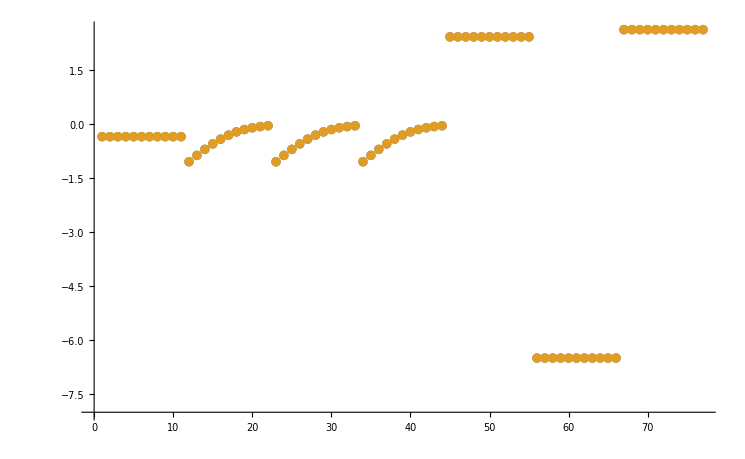

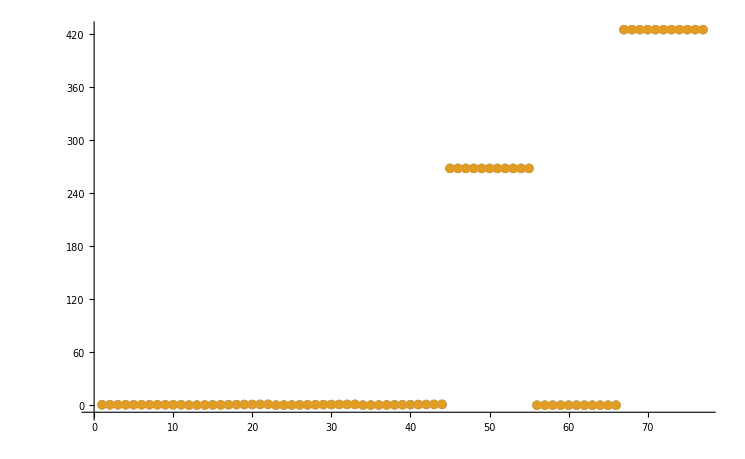

```mathematica
dataSetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

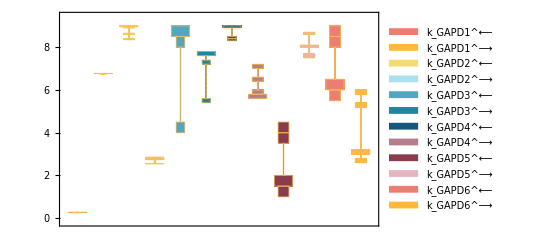

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

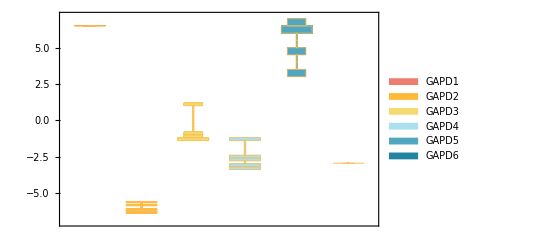

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

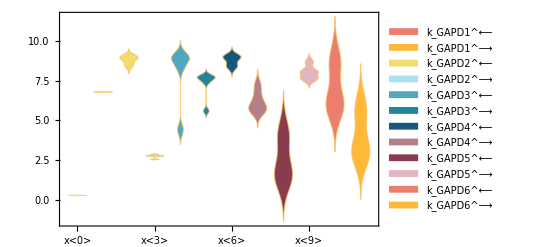

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

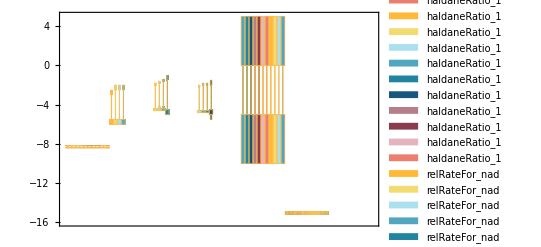

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePathList][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000045 | 0.000044999 | 0.00221259
0.00089 | 0.000889608 | 0.0440734
0.00053 | 0.000529863 | 0.0259159

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 7.91258×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 1.40397×10^-6

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

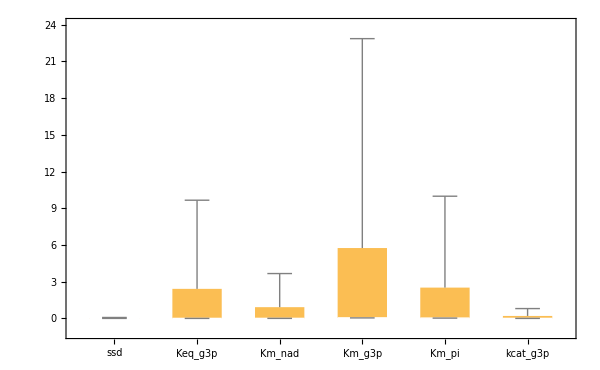

```mathematica
dataHeader = Import[dataFilePathList][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```